```mathematica
xephotoion=Import["/Users/Max/ownCloud/Doktor/Thesis/calculations/xe.txt","Data"];
hephotoion=Import["/Users/Max/ownCloud/Doktor/Thesis/calculations/he.txt","Data"];
xeindex=Import["/Users/Max/ownCloud/Doktor/Thesis/calculations/xenon-refractive-index.dat","Data"];
heindex=Import["/Users/Max/ownCloud/Doktor/Thesis/calculations/helium-refractive-index.dat","Data"];
```

```mathematica
xephotoion//Dimensions
hephotoion//Dimensions
```

{186,2}

{105,2}

```mathematica
xeindex[[3]]
xeindex[[3]][[3]]
```

{30.,0.116491,0.0421932}

0.0421932

```mathematica
xedelta=Table[{xeindex[[x]][[1]],xeindex[[x]][[2]]},{x,3,Length[xeindex]}];
xebeta=Table[{xeindex[[x]][[1]],xeindex[[x]][[3]]},{x,3,Length[xeindex]}];
hedelta=Table[{heindex[[x]][[1]],heindex[[x]][[2]]},{x,3,Length[heindex]}];
hebeta=Table[{heindex[[x]][[1]],heindex[[x]][[3]]},{x,3,Length[heindex]}];
```

```mathematica
Needs["PlotLegends`"]
```

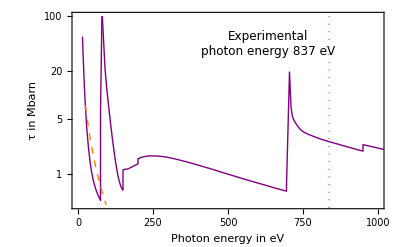

```mathematica
ListLogPlot[{xephotoion,hephotoion},Joined->True,PlotRange->{{0,1000},{0.4,100}},Frame->True,PlotStyle->{Directive[Thick,Purple],Directive[Thick,Dashed,Orange]},FrameLabel->{"Photon energy in eV","τ in Mbarn"},FrameStyle->Directive[12],Epilog->{{Directive[Red, Thick, Dotted],Line[{{837,-1},{837.1,100}}]},{Text[Style["Experimental\nphoton energy 837 eV",FontSize->12,TextAlignment->Right],{635,3.8}]}}]
```

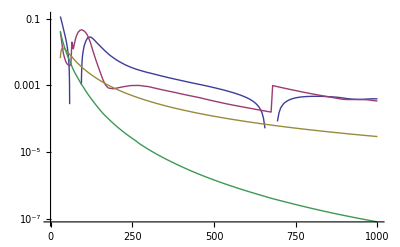

```mathematica
ListLogPlot[{xedelta,xebeta,hedelta,hebeta},Joined->True]
```